## Single Soliton

Checking we have the correct constants for a single soliton.   Our equation is 
	u_t+6 u u_x+u_xxx=0

```mathematica
Clear[x,t]
uSoliton[c_][x_,t_]:=c/2 Sech[(√c)/2(x-c t)]^2
```

Checking the formula and looking at the forms.

0

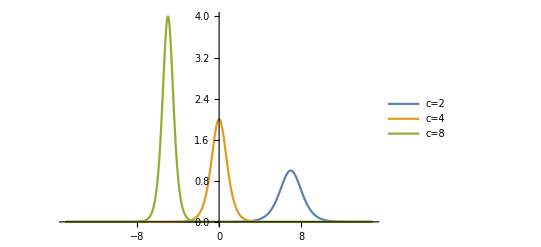

```mathematica
L=30;
Hmm=Simplify[
D[uSoliton[c][x,t],t]+
6 uSoliton[c][x,t]*D[uSoliton[c][x,t],x]+
D[uSoliton[c][x,t],{x,3}]]
Plot[{uSoliton[2][x-7,0],uSoliton[4][x,0],uSoliton[8][x+5,0]},{x,-L/2,L/2},
PlotRange->All,
PlotLegends->{"c=2","c=4","c=8"}]
```

```mathematica
Manipulate[
 Plot[{uSoliton[2][x-7-2 t,0],uSoliton[4][x-4t,0],uSoliton[8][x+5-8t,0]},{x,-L/2,L/2},
PlotRange->All,
PlotLegends->{"c=8","c=4","c=2"}],
{t,0, 2,0.01}]
```

```mathematica
Test=Table[
 Plot[{uSoliton[2][x-7-2 t,0],uSoliton[4][x-4t,0],uSoliton[8][x+5-8t,0]},{x,-L/2,L/2},
PlotRange->All,
PlotLegends->{"c=8","c=4","c=2"}],
{t,0, 2,0.01}]
SetDirectory["C:\\Users\\AllanStruthers\\Desktop\\GitHub\\Spring_2026_Courses\\PDE\\Week 14"]
Export["Test.gif",Test]
```

C:\Users\AllanStruthers\Desktop\GitHub\Spring_2026_Courses\PDE\Week 14

We would like to make our analytic solutions march of one side and come back in on the other.   How should we do this.  Our FFT based numerics should do it automatically!

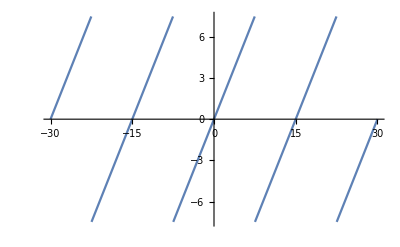

```mathematica
L=15;
Plot[Mod[x,L,L/2]-L,{x, -2L, 2L}]
```

```mathematica
Manipulate[
 Plot[{uSoliton[2][Mod[x-7-2 t,L,L/2]-L,0]},{x,-L/2,L/2},
PlotRange->{0,1},
PlotLegends->{"c=2"}],
{t,0, 10,0.2}]
```

## Numerics

Checking that the sampling and differentiation formulas are correct. I made sure everything was a floating point number by putting decimal points in the appropriate pieces.

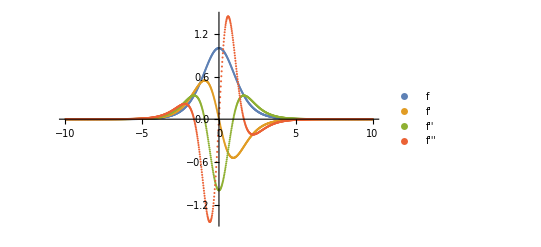

```mathematica
Clear[n,L,T,dx,dt,x,k]
(* AAS Combined defs for space. I think interval is -L/2 < x< L/2, eliminated cfl and just defined dx and dt *)
{n,L,T}={2*512,20.0,1.35264};
{dx,dt}={L/n,0.1};
(* AAS added decimal points to make sure they are floats. Visually checked k *)
x = Table[-L/2.0+i*dx,{i,1,n}];
(* Define a soliton profile for an IC *)
f[x_]:=uSoliton[2][x,0]
(* AAS: f is a function. u is a vector of function values *)
u=f[x];
uP=f'[x];
uPP=f''[x];
uPPP=f'''[x];
ListPlot[{{x,u}ᵀ,{x,uP}ᵀ,{x,uPP}ᵀ,{x,uPPP}ᵀ},
PlotRange->All,
PlotLegends->{"f","f'","f''","f'''"}]
```

Check that we can compute derivatives correctly.  If we include all the modes the noise in the high frequency modes gets amplified badly.  Those high frequency modes are localized at the ends of our interval.

```mathematica
(* AAS: reordered the wave numbers to be in the standard (all be it weird) order *)
(* AAS: zeroed out the Highest Nyquist frequency *)
(* AAS: Take a look at the k to see the only change *)
k = Join[Range[0,n/2-1],{0},Range[1-n/2,-1,1]];
(* AAS: Not sure if I messed up the 2 or it was in what you sent me *)
DerMul1=-ⅈ k*(2π)/L; DerMul2=DerMul1^2;DerMul3=DerMul1^3;
uF=Fourier[u];
up=InverseFourier[DerMul1*uF];
upp=InverseFourier[DerMul2*uF];
uppp=InverseFourier[DerMul3*uF];
TabView[{
"Pow Spec u"->ListLogPlot[Abs[uF],GridLines->{{n/3,2 n/3},Automatic}],
"F Ders"->ListPlot[{{x,up}ᵀ,{x,upp}ᵀ,{x,uppp}ᵀ},
PlotLegends->{"1st Der","2nd Der","3rd Der"},PlotRange->All],
"Der Errs"->ListLogPlot[{{x,Abs[up-uP]}ᵀ,{x,Abs[upp-uPP]}ᵀ,{x,Abs[uppp-uPPP]}ᵀ},
PlotLegends->{"1st Der Err","2nd Der Err","3rd Der Err"},
GridLines->Automatic]
},2]
```

123

There is a simple brutal solution to the amplification of the high frequencies. Zero out the middle chunk of high frequencies in the FFT and take the real part if you need to.

```mathematica
(* AAS: reordered the wave numbers to be in the standard (all be it weird order *)
(* AAS: zeroed out the Highest Nyquist frequency *)
(* AAS: Take a look at the k to see the only change *)
k = Join[Range[0,n/2-1],{0},Range[1-n/2,-1,1]];
mask=Map[Boole[Abs[#]<n/3]&,k];
(* AAS: Not sure if I messed up the 2 or it was in what you sent me *)
DerMul1=-ⅈ k*(2π)/L; DerMul2=DerMul1^2;DerMul3=DerMul1^3;
uF=mask*Fourier[u];
up=Re[InverseFourier[DerMul1*uF]];
upp=Re[InverseFourier[DerMul2*uF]];
uppp=Re[InverseFourier[DerMul3*uF]];
TabView[{
"Pow Spec u"->ListLogPlot[Abs[uF],GridLines->{{n/3,2 n/3},Automatic}],
"F Ders"->ListPlot[{{x,up}ᵀ,{x,upp}ᵀ,{x,uppp}ᵀ},
PlotLegends->{"1st Der","2nd Der","3rd Der"},PlotRange->All],
"Der Errs"->ListLogPlot[{{x,Abs[up-uP]}ᵀ,{x,Abs[upp-uPP]}ᵀ,{x,Abs[uppp-uPPP]}ᵀ},
PlotLegends->{"1st Der Err","2nd Der Err","3rd Der Err"}]
},2]
```

123

The other advantage of throwing away the highest frequencies is that if you do not the run out of frequencies when you multiply the function by its derivative.